```mathematica
Quit[];
```

## QCD

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
1/(4Pi N)/.N:>5//N
```

0.0159155

```mathematica
αs[MZ]/5
```

0.0236576

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

```mathematica
nfTab={3,3,3,3,4,5,5};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.378129,0.378129,0.378129,0.378129,0.303565,0.213,0.213}

{0.335423,0.335423,0.335423,0.335423,0.299152,0.217435,0.217435}

{0.386001,0.386001,0.386001,0.386001,0.332194,0.229911,0.229911}

{0.147643,0.147643,0.147643,0.147643,0.122648,0.0893248,0.0893248}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.398031,0.504173,0.756259,1.51252,6.07131,21.3,213.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.353077,0.447231,0.670847,1.34169,5.98303,21.7435,217.435}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.406317,0.514668,0.772002,1.544,6.64387,22.9911,229.911}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.155414,0.196857,0.295286,0.590571,2.45297,8.93248,89.3248}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{175565.,8.76424,0.344226,0.337729,0.202298,0.151919,0.105198}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6578.04,10.0428,0.878876,0.373108,0.204763,0.152134,0.105092}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{135.103,4.03082,0.830355,0.372494,0.200221,0.150653,0.104287}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.503596,0.251685,0.177962,0.118641}

```mathematica
αs[1]
```

0.395109

```mathematica
αs3Loop[1]
```

0.47641

```mathematica
αs2Loop[1]
```

0.545637

```mathematica
αs1Loop[1]
```

0.364949

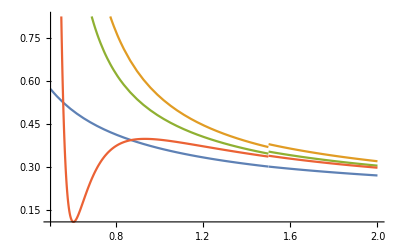

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

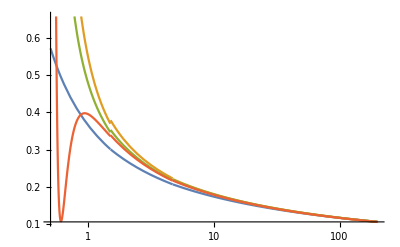

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

## dQCD

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

### Nd=3

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.16074

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.07884

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211767

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231173

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650813

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.183929

0.193995

0.198324

0.16676

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08325

6.48864

23.0481

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1942

20.3311

72.2174

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

818.54

749.827

2663.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222913,0.282356,0.423534,0.847069,4.23534,21.1767,211.767}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.24334,0.308231,0.462347,0.924693,4.62347,23.1173,231.173}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685066,0.0867751,0.130163,0.260325,1.30163,6.50813,65.0813}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{181472.,10.4543,0.237118,0.267327,0.14756,0.101565,0.0707307}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6214.1,9.42661,0.748873,0.304487,0.149909,0.102174,0.0709126}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{25.3853,2.69684,0.712084,0.307309,0.14697,0.100342,0.0699798}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{11.1359,1.98552,0.824065,0.412033,0.190671,0.124034,0.0826895}

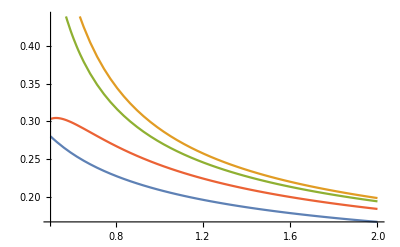

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

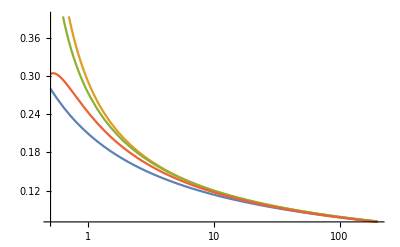

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### Nd=4

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>4;
β1N=beta1/.N:>4;
β2N=beta2/.N:>4;
β3N=beta3/.N:>4;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.12061

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0591321

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211638

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23123

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.065098

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>4;
β1N=beta1/.N:>4;
β2N=beta2/.N:>4;
β3N=beta3/.N:>4;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.138051

0.14546

0.148769

0.12508

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08757

6.48706

23.0422

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2077

20.3261

72.1988

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.039

749.645

2662.75

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211638,0.211638,0.211638,0.211638,0.211638,0.211638,0.211638}

{0.23123,0.23123,0.23123,0.23123,0.23123,0.23123,0.23123}

{0.065098,0.065098,0.065098,0.065098,0.065098,0.065098,0.065098}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222777,0.282184,0.423277,0.846553,4.23277,21.1638,211.638}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.2434,0.308306,0.462459,0.924918,4.62459,23.123,231.23}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685243,0.0867974,0.130196,0.260392,1.30196,6.5098,65.098}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{136531.,8.27155,0.190622,0.201294,0.110706,0.0761801,0.0530493}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{4660.57,7.06996,0.561655,0.228365,0.112432,0.0766305,0.0531844}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{19.0125,2.02203,0.534111,0.230506,0.110233,0.0752586,0.0524855}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{8.35195,1.48914,0.618049,0.309025,0.143003,0.0930257,0.0620171}

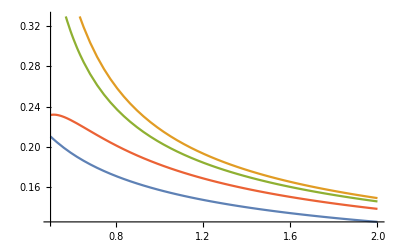

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

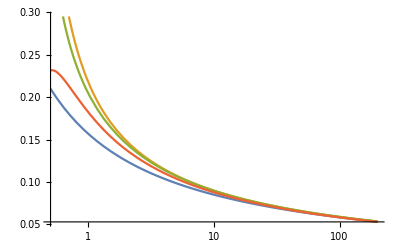

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### Nd=5

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>5;
β1N=beta1/.N:>5;
β2N=beta2/.N:>5;
β3N=beta3/.N:>5;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.0965081

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0473065

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211579

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231256

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0651058

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>5;
β1N=beta1/.N:>5;
β2N=beta2/.N:>5;
β3N=beta3/.N:>5;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.11048

0.116355

0.119025

0.100067

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08956

6.48633

23.0394

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.214

20.3238

72.1902

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.27

749.56

2662.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211579,0.211579,0.211579,0.211579,0.211579,0.211579,0.211579}

{0.231256,0.231256,0.231256,0.231256,0.231256,0.231256,0.231256}

{0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222714,0.282105,0.423157,0.846314,4.23157,21.1579,211.579}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243427,0.308341,0.462511,0.925022,4.62511,23.1256,231.256}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685324,0.0868077,0.130212,0.260423,1.30212,6.51058,65.1058}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{109382.,6.77677,0.157231,0.161331,0.0885787,0.0609465,0.04244}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3728.46,5.65597,0.449324,0.182692,0.0899454,0.0613044,0.0425475}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{15.2003,1.6174,0.427307,0.184414,0.0881881,0.0602076,0.0419887}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{6.68156,1.19131,0.494439,0.24722,0.114402,0.0744205,0.0496137}

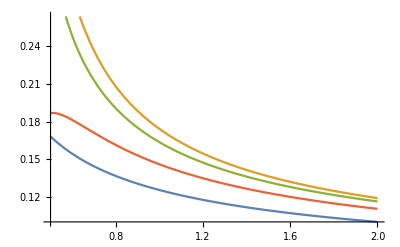

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

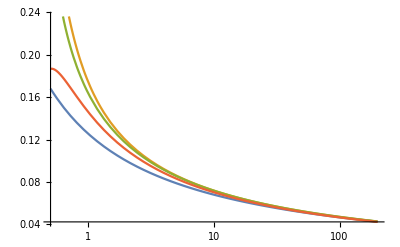

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### Nd=6

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>6;
β1N=beta1/.N:>6;
β2N=beta2/.N:>6;
β3N=beta3/.N:>6;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.0804326

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0394224

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211546

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23127

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.06511

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>6;
β1N=beta1/.N:>6;
β2N=beta2/.N:>6;
β3N=beta3/.N:>6;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0920842

0.0969567

0.0991921

0.0833909

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.09065

6.48593

23.0379

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2174

20.3226

72.1855

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.396

749.515

2662.26

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211546,0.211546,0.211546,0.211546,0.211546,0.211546,0.211546}

{0.23127,0.23127,0.23127,0.23127,0.23127,0.23127,0.23127}

{0.06511,0.06511,0.06511,0.06511,0.06511,0.06511,0.06511}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.22268,0.282062,0.423092,0.846185,4.23092,21.1546,211.546}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243442,0.30836,0.462539,0.925079,4.62539,23.127,231.27}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685368,0.0868133,0.13022,0.26044,1.3022,6.511,65.11}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{91223.4,5.71952,0.133169,0.134577,0.0738217,0.0507898,0.0353668}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3107.05,4.7133,0.374437,0.152243,0.0749545,0.051087,0.0354563}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{12.6625,1.34774,0.356097,0.153683,0.073491,0.0501733,0.0349907}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{5.56797,0.99276,0.412033,0.206016,0.0953354,0.0620171,0.0413447}

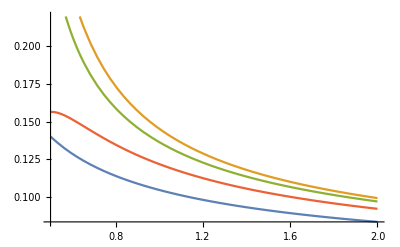

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

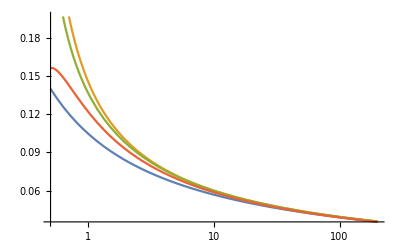

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### Nd=100

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>100;
β1N=beta1/.N:>100;
β2N=beta2/.N:>100;
β3N=beta3/.N:>100;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.00482721

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.00236539

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211473

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231302

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0651195

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>100;
β1N=beta1/.N:>100;
β2N=beta2/.N:>100;
β3N=beta3/.N:>100;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.00552745

0.00581659

0.00595212

0.00500367

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.09311

6.48504

23.0346

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2251

20.3198

72.175

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.68

749.411

2661.87

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473}

{0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302}

{0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222603,0.281964,0.422946,0.845891,4.22946,21.1473,211.473}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243475,0.308402,0.462603,0.925207,4.62603,23.1302,231.302}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685469,0.0868261,0.130239,0.260478,1.30239,6.51195,65.1195}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{5483.11,0.352983,0.00828125,0.00809279,0.00443014,0.00304754,0.00212204}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{186.423,0.282798,0.0224662,0.0091346,0.00449727,0.00306522,0.00212738}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.759149,0.0808505,0.021367,0.00922154,0.00440957,0.00301044,0.00209946}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.334078,0.0595656,0.024722,0.012361,0.00572012,0.00372103,0.00248068}

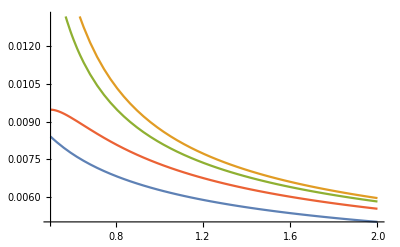

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

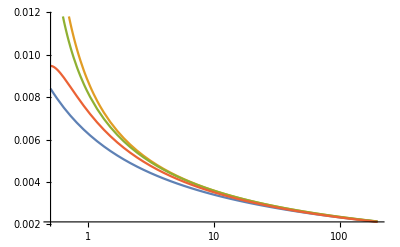

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```